Comparison between the two bases for polynomials

5

{1,p,p^2,p^3,p^4,p^5}

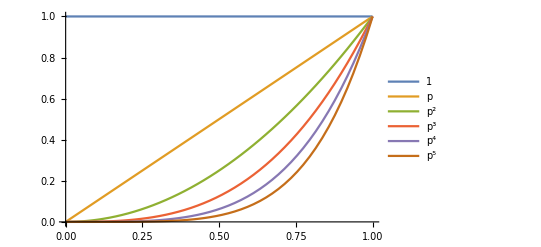

{(1-p)^5,(1-p)^4 p,(1-p)^3 p^2,(1-p)^2 p^3,(1-p) p^4,p^5}

{(1-p)^5,5 (1-p)^4 p,10 (1-p)^3 p^2,10 (1-p)^2 p^3,5 (1-p) p^4,p^5}

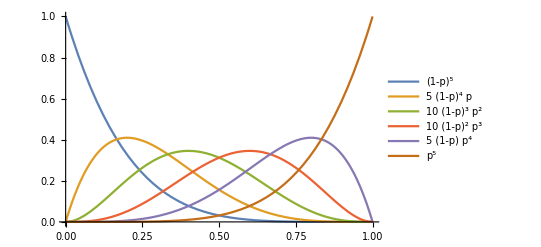

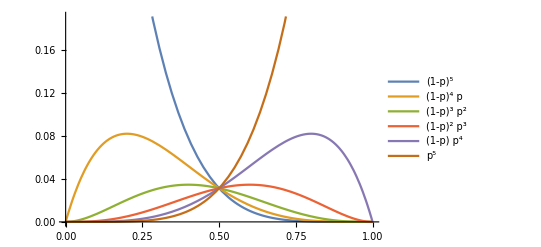

```mathematica
n = 5
pbase = Table[p^i,{i,0,n}]
Plot[pbase,{p,0,1}, PlotLegends->"Expressions"]
basef[i_,m_,p_]=p^i(1-p)^(m-i);
base = Table[basef[i,n,p],{i,0,n}]
basescale = Table[Binomial[n,i]*basef[i,n,p],{i,0,n}]
Plot[basescale,{p,0,1},PlotLegends->"Expressions",PlotRange->All]
Plot[base,{p,0,1},PlotLegends->"Expressions"]
```